## Example notebook for 2D figures

This notebook shows how to produce Fig. 14 of the dynamical systems review [arXiv:1712.03107]

#### Equations:

The autonomous equations are the following:

```mathematica
Eqx=1/2 (3 (-1+w) x[η]^3-√6 λ y[η]^2-3 x[η] (1-w+(1+w) y[η]^2));
Eqy=-1/2 y[η] (√6 λ x[η]-3 (-1+w) x[η]^2+3 (1+w) (-1+y[η]^2));
```

```mathematica
ex=Eqx/.x_[η]->x
ey=Eqy/.x_[η]->x
```

1/2 (3 (-1+w) x^3-3 x (1-w+(1+w) y^2)-√6 y^2 λ)

-1/2 y (-3 (-1+w) x^2+3 (1+w) (-1+y^2)+√6 x λ)

Defition of some relevant physical quantities:

```mathematica
Ωphi=-x^2+y^2;
Ωm=1-Ωphi;
```

```mathematica
wphi=(-x^2-y^2)/(-x^2+y^2);
```

```mathematica
weff=Ωphi wphi + Ωm w ;
```

Selecting the parameters:

```mathematica
w=0;
λ=1;
```

#### Phase space boundaries:

Plotting the boundaries of the phase space:

```mathematica
boundsf=RegionPlot[Y^2-X^2<1&&Y>0,{X,-5,5},{Y,0,4},PlotStyle->None,BoundaryStyle->Thickness[0.003]];
```

#### Critical points:

Plotting the critical points:

```mathematica
cp=Graphics[{PointSize[0.02],Point[{0,0}],Point[{-λ/(√6),(√(6+λ^2))/(√6)}]}];
```

#### Heteroclinic orbit between points O and C:

Plotting some orbits:

```mathematica
nsol=NDSolve[Evaluate[{{Eqx==x'[η],Eqy==y'[η]}, x[0]==0,y[0]==0.01}], {x[η], y[η]}, {η, 0, 100},MaxSteps->10^5,StartingStepSize->0.001,MaxStepFraction->1/1000]
```

{{x[η]→InterpolatingFunction[{{0.,100.}},<>][η],y[η]→InterpolatingFunction[{{0.,100.}},<>][η]}}

```mathematica
pt=ParametricPlot[Evaluate[
{Re[x[η]],Re[y[η]]}/.nsol[[1]]],
 {η,0, 100},PlotPoints -> 200,PlotStyle->{Red,Thick,Dashed}];
```

#### Point labels:

Plotting the lables for the critical points:

```mathematica
labelsf=Graphics[{Text[Style["O",70],{0,0},{-1,-1}],Text[Style["C",70],{-λ/(√6),(√(6+λ^2))/(√6)},{0,-1}]}];
```

#### Phantom and acceleration region:

Plotting the phantom and acceleration regions:

```mathematica
phantom=RegionPlot[-x^2+y^2≤1&&y>0&&weff<-1,{x,-5,5},{y,0,4},PlotPoints->100,PlotStyle->RGBColor[0.45, 1, 0.4],BoundaryStyle->None,Frame->True,Axes->False,FrameLabel->{X,Y},FrameStyle->30,RotateLabel->False,AspectRatio->1/2,ImageSize->1000];
acc=RegionPlot[-x^2+y^2≤1&&y>0&&-1<weff<-1/3,{x,-5,5},{y,0,4},PlotPoints->50,PlotStyle->{Yellow},BoundaryStyle->None,Frame->True,Axes->False,FrameLabel->{X,Y},FrameStyle->30,RotateLabel->False,AspectRatio->1/2,ImageSize->1000];
```

#### Stream Plot:

Making the stream plot:

```mathematica
st=StreamPlot[{ex,ey},{x,-2,2},{y,0,2},RegionFunction->Function[{X,Y},Y^2-X^2<1&&Y>0],AspectRatio->1/2,ImageSize->1000,Frame->True,Axes->False,FrameLabel->{x,y},FrameStyle->30,RotateLabel->False];
```

#### Making the figure :

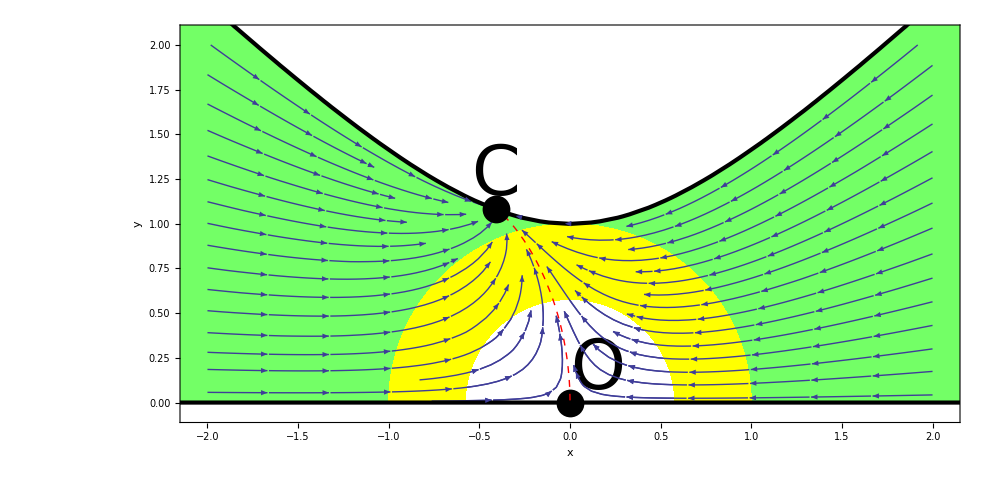

```mathematica
Show[st,phantom,acc,st,pt,boundsf,cp,labelsf]
```

#### Saving the figure:

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Filename.pdf",Show[st,phantom,acc,st,pt,boundsf,cp,labelsf]]
```

Filename.pdf